```mathematica
perm = Permutations[Range[6]];
V=1;
```

```mathematica
Energy[state_,ρ1_]:=V/2*(Sum[(config[[i]]+config[[i+1]]-1-ρ1)^2,{i,1,5}] +(config[[1]]+config[[6]]-1-ρ1)^2);
E0[ρ1_]:=3 V ρ1^2;
```

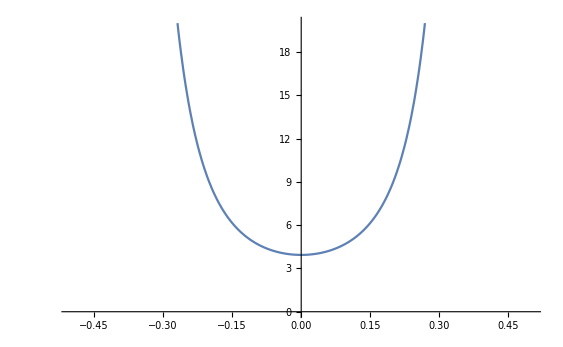

```mathematica
total = 0;
For[p=1,p<=Factorial[6],p++,config={0,1,0,1,0,1};
prod =1;
For[j=1,j<6,j++,config[[perm[[p]][[j]]]]=1-config[[perm[[p]][[j]]]];
prod = prod/(Energy[config,ρ1]-E0[ρ1])];
total = total+prod;];
total;
Jring = (1/2^6)*total;
Plot[Jring,{ρ1,-0.5,0.5},PlotRange->{0,20}]
```

```mathematica
Jring/.{ρ1->0}
Jring/.{ρ1->0.2}
```

63/16

8.99616

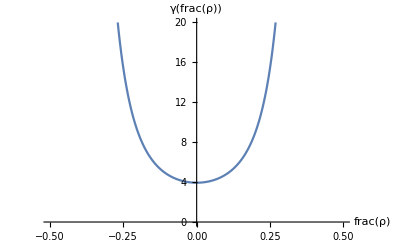

/Users/jeet/umd/acad/projects/quantum_spin_liquids/notes/old_compact_gauge_theory/images/drawing_board/code/Jring.pdf

```mathematica
Plot[Jring,{ρ1,-0.5,0.5},PlotRange->{0,20},AxesLabel->{"frac(ρ)","γ(frac(ρ))"},LabelStyle->Directive[Medium]]
Export[NotebookDirectory[]<>"Jring.pdf",%]
```

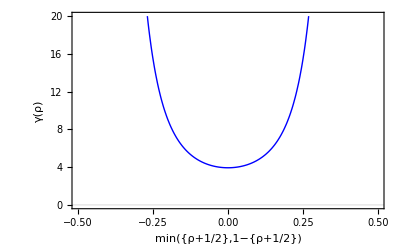

```mathematica
Plot[Jring,{ρ1,-0.5,0.5},PlotRange->{0,20},FrameLabel->{"min({ρ+1/2},1−{ρ+1/2})","γ(ρ)"},Frame->True,BaseStyle->{FontFamily->"Times New Roman",18},LabelStyle->{FontFamily->"Times New Roman"},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Blue,Thick}},PlotTheme->"Scientific",GridLines->{None,{0}}]
Export[NotebookDirectory[]<>"Jring.pdf",%]
```

```mathematica
ρ-nint(ρ)
```